```mathematica
(*Author : Oleg Kravchenko, 11/09/15*)
```

```mathematica
ClearAll["Global`*"]
```

### CIP - BS plots; Ref: NIFS-778, Basis Set Approach in the Constrained Interpolation Profile Method, T. Utsumi, J. Koga, T. Yabe, Y. Ogata, E. Matsunaga, T. Aoki and M. Sekine, July 2003

### Parameters;

```mathematica
ImgSz=250;
```

### Basic Functions;

```mathematica
θ[x_]:=HeavisideTheta[x]-HeavisideTheta[x-1]
(*ϕK[x_,K_]:=Sum[Subscript[a, k] x^k,{k,0,2K+1,1}]
BasisCIPBS[x_,K_]:=Module[{ϕList,ϕL,ϕR,ϕ},
ϕK[x,K]:=Sum[Subscript[a, k] x^k,{k,0,2K+1,1}];
EqnSysL[K]:={
(D[ϕK[x,K],{x,0}]/.x->0)==1,
Table[(D[ϕK[x,K],{x,l}]/.x->0)==0,{l,1,K,1}],
Table[(D[ϕK[x,K],{x,l}]/.x->-h)==0,{l,0,K,1}]
}//Flatten;
EqnSysR[K]:={
(D[ϕK[x,K],{x,0}]/.x->0)==1,
Table[(D[ϕK[x,K],{x,l}]/.x->0)==0,{l,1,K,1}],
Table[(D[ϕK[x,K],{x,l}]/.x->h)==0,{l,0,K,1}]
}//Flatten;
ϕList={
ϕL=ϕK[x,K]/.Solve[EqnSysL[K],CoefficientList[ϕK[x,K],x]] ,
ϕR=ϕK[x,K]/.Solve[EqnSysR[K],CoefficientList[ϕK[x,K],x]],
ϕ=ϕL θ[x+1]+ϕR θ[x]
}//Flatten
];
Row@{Plot[Evaluate[BasisCIPBS[x,0]/.h->1//Last],{x,-2,2},ImageSize->ImgSz],Plot[{θ[x+1],θ[x]},{x,-2,2},ImageSize->ImgSz]}*)
```

```mathematica
BasisCIPBS[x_,k_,K_]:=Module[{ϕList,ϕL,ϕR,ϕ},
ϕK[x,K]:=Sum[Subscript[a, i] x^i,{i,0,2K+1,1}];
EqnSysL[k,K]:={
Table[If[l==k,(D[ϕK[x,K],{x,l}]/.x->0)==1,(D[ϕK[x,K],{x,l}]/.x->0)==0],{l,0,K,1}],
Table[(D[ϕK[x,K],{x,l}]/.x->-h)==0,{l,0,K,1}]
}//Flatten;
EqnSysR[k,K]:={
Table[If[l==k,(D[ϕK[x,K],{x,l}]/.x->0)==1,(D[ϕK[x,K],{x,l}]/.x->0)==0],{l,0,K,1}],
Table[(D[ϕK[x,K],{x,l}]/.x->h)==0,{l,0,K,1}]
}//Flatten;
ϕList={
ϕL=ϕK[x,K]/.Solve[EqnSysL[k,K],CoefficientList[ϕK[x,K],x]] ,
ϕR=ϕK[x,K]/.Solve[EqnSysR[k,K],CoefficientList[ϕK[x,K],x]],
(*ϕ=ϕL θ[x+1]+ϕR θ[x]*)
ϕ=Piecewise[{
{ϕL[[1]],-h≤x≤0},
{ϕR[[1]],0≤x≤h}
}]
}//Flatten
]
```

#### Manipulation;

```mathematica
Manipulate[Column[{BasisCIPBS[x,k,indK][[1;;2]]//Column,
Plot[Evaluate[BasisCIPBS[x,k,indK][[3]]/.h->1],{x,-1,1},ImageSize->ImgSz]},Alignment->Center],
{{indK,0,"K"},0,7,1},{k,0,indK,1}]
```

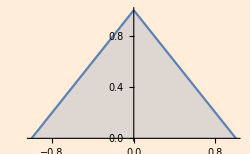
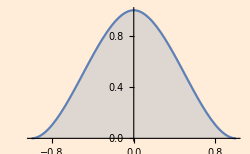
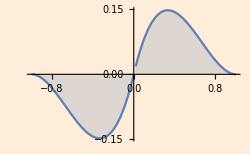
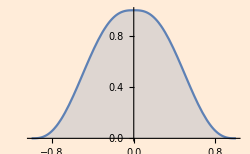
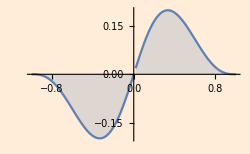
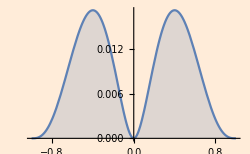
1+x
1-x
-Graphics-
		1-3 x^2-2 x^3
1-3 x^2+2 x^3
-Graphics-x+2 x^2+x^3
x-2 x^2+x^3
-Graphics-
		1+10 x^3+15 x^4+6 x^5
1-10 x^3+15 x^4-6 x^5
-Graphics-x-6 x^3-8 x^4-3 x^5
x-6 x^3+8 x^4-3 x^5
-Graphics-x^2/2+(3 x^3)/2+(3 x^4)/2+x^5/2
x^2/2-(3 x^3)/2+(3 x^4)/2-x^5/2
-Graphics-

Export::nodir: Directory "C:\\Users\\Oleg\\Dropbox\\Collaboration\\nb\\img\\png\\" does not exist.

Export::noopen: Cannot open "C://Users//Oleg//Dropbox//Collaboration//nb//img//png//CIPBS2.png".

$Failed

```mathematica
(*KMax=2;
t=Table[Column[{BasisCIPBS[x,k,indK][[1;;2]]/.h->1//Column,
Plot[Evaluate[BasisCIPBS[x,k,indK][[3]]/.h->1],{x,-1,1},ImageSize->ImgSz,PlotStyle->Thick,Filling->Axis,Background->Lighter[Orange, 0.85]]},Alignment->Center],
{indK,0,KMax,1},{k,0,indK,1}];
tImg={Row[#,"\t"]}&/@t//Grid
Export["C://Users//Oleg//Dropbox//Collaboration//nb//img//png//CIPBS"<>ToString[KMax]<>".png",tImg]*)
```

### Integrals;

```mathematica
indK=2;
{
ϕList=Table[BasisCIPBS[x,k,indK][[3]],{k,0,indK}],
d1ϕList=D[ϕList,{x,1}]//Evaluate//Simplify,
d2ϕList=D[ϕList,{x,2}]//Evaluate//Simplify
}//Flatten

(*Manipulate[Table[Integrate[ϕList[[1]](ϕList[[j]]/.x->x+shift h)/.h->1,{x,-1,1}]//Evaluate,{shift,-1,1}],{j,1,2indK,1}]*)

bsTbl0=Table[Integrate[ϕList[[i]](ϕList[[j]]/.x->x+shift h)/.h->1,{x,-1,1}],{j,1,indK+1},{i,1,indK+1},{shift,-1,1,1}];
bsTbl1=Table[Integrate[ϕList[[i]](d1ϕList[[j]]/.x->x+shift h)/.h->1,{x,-1,1}],{i,1,indK+1},{j,1,indK+1},{shift,-1,1,1}];
bsTbl2=Table[Integrate[ϕList[[i]](d2ϕList[[j]]/.x->x+shift h)/.h->1,{x,-1,1}],{i,1,indK+1},{j,1,indK+1},{shift,-1,1,1}];

bsTbl=Flatten[{bsTbl0,bsTbl1,bsTbl2},1];
ttt=Grid[Flatten[bsTbl,1],
Background->{{{Lighter[Gray,.8],Lighter[Green,.8]}},None},Spacings->{2,2},ItemStyle->18]
```

{Piecewise[{{1+(10 x^3)/h^3+(15 x^4)/h^4+(6 x^5)/h^5, -h≤x≤0}, {1-(10 x^3)/h^3+(15 x^4)/h^4-(6 x^5)/h^5, 0≤x≤h}, {0, True}}],Piecewise[{{x-(6 x^3)/h^2-(8 x^4)/h^3-(3 x^5)/h^4, -h≤x≤0}, {x-(6 x^3)/h^2+(8 x^4)/h^3-(3 x^5)/h^4, 0≤x≤h}, {0, True}}],Piecewise[{{x^2/2+(3 x^3)/(2 h)+(3 x^4)/(2 h^2)+x^5/(2 h^3), -h≤x≤0}, {x^2/2-(3 x^3)/(2 h)+(3 x^4)/(2 h^2)-x^5/(2 h^3), 0≤x≤h}, {0, True}}],Piecewise[{{(30 x^2 (h+x)^2)/h^5, h+x≥0&&x≤0}, {-(30 (h-x)^2 x^2)/h^5, x≥0&&h≥x}, {0, True}}],Piecewise[{{((h+x)^2 (h^2-2 h x-15 x^2))/h^4, h+x≥0&&x≤0}, {((h-x)^2 (h^2+2 h x-15 x^2))/h^4, x≥0&&h≥x}, {0, True}}],Piecewise[{{(x (h+x)^2 (2 h+5 x))/(2 h^3), h+x≥0&&x≤0}, {((2 h-5 x) (h-x)^2 x)/(2 h^3), x≥0&&h≥x}, {0, True}}],Piecewise[{{(60 x (h^2+3 h x+2 x^2))/h^5, h+x≥0&&x≤0}, {-(60 x (h^2-3 h x+2 x^2))/h^5, x≥0&&h≥x}, {0, True}}],Piecewise[{{-(12 x (3 h^2+8 h x+5 x^2))/h^4, h+x≥0&&x≤0}, {-(12 x (3 h^2-8 h x+5 x^2))/h^4, x≥0&&h≥x}, {0, True}}],Piecewise[{{(h^3+9 h^2 x+18 h x^2+10 x^3)/h^3, h+x≥0&&x≤0}, {(h^3-9 h^2 x+18 h x^2-10 x^3)/h^3, x≥0&&h≥x}, {0, True}}]}

25/231 | 181/231 | 25/231
151/4620 | 0 | -151/4620
181/55440 | 281/27720 | 181/55440
-151/4620 | 0 | 151/4620
-19/1980 | 104/3465 | -19/1980
-13/13860 | 0 | 13/13860
181/55440 | 281/27720 | 181/55440
13/13860 | 0 | -13/13860
1/11088 | 1/4620 | 1/11088
1/2 | 0 | -1/2
-11/84 | 11/42 | -11/84
1/84 | 0 | -1/84
11/84 | -11/42 | 11/84
-13/420 | 0 | 13/420
13/5040 | 1/504 | 13/5040
1/84 | 0 | -1/84
-13/5040 | -1/504 | -13/5040
1/5040 | 0 | -1/5040
10/7 | -20/7 | 10/7
-3/14 | 0 | 3/14
1/84 | -1/42 | 1/84
3/14 | 0 | -3/14
1/70 | -16/35 | 1/70
-1/210 | 0 | 1/210
1/84 | -1/42 | 1/84
1/210 | 0 | -1/210
-1/1260 | -1/315 | -1/1260

### CIP-BS^0;

```mathematica
ϕ0m[x_,ξ_,dx_]:=1+1/dx(x-ξ)
ϕ0p[x_,ξ_,dx_]:=1-1/dx(x-ξ)
```

```mathematica
ϕ0[x_,ξ_,dx_]:=ϕ0m[x,ξ,dx]θ[ξ+1]+ϕ0p[x,ξ,dx]θ[ξ]
```

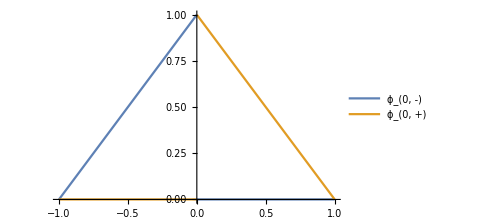

```mathematica
Plot[{ϕ0m[x,0,1]θ[x+1],ϕ0p[x,0,1]θ[x]},{x,-1,1},PlotRange->Full,ImageSize->Medium,PlotLegends->{"ϕ_(0, -)","ϕ_(0, +)"}]
```

#### CIP-BS^1;

```mathematica
ϕ0m[x_,ξ_,dx_]:=1-3/dx^2(x-ξ)^2-2/dx^3(x-ξ)^3
ϕ0p[x_,ξ_,dx_]:=1-3/dx^2(x-ξ)^2+2/dx^3(x-ξ)^3
ϕ1m[x_,ξ_,dx_]:=x-ξ+2/dx(x-ξ)^2+1/dx^2(x-ξ)^3
ϕ1p[x_,ξ_,dx_]:=x-ξ-2/dx(x-ξ)^2+1/dx^2(x-ξ)^3
```

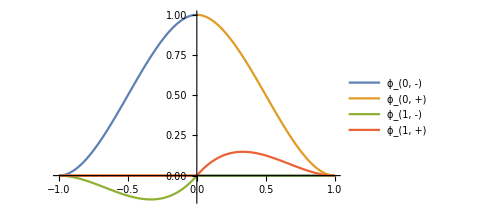

```mathematica
Plot[{ϕ0m[x,0,1]θ[x+1],ϕ0p[x,0,1]θ[x],ϕ1m[x,0,1]θ[x+1],ϕ1p[x,0,1]θ[x]},{x,-1,1},PlotRange->Full,ImageSize->Medium,PlotLegends->{"ϕ_(0, -)","ϕ_(0, +)","ϕ_(1, -)","ϕ_(1, +)"}]
```

#### CIP-BS^2;

```mathematica
ϕ0m[x_,ξ_,dx_]:=1+10/dx^3(x-ξ)^3+15/dx^4(x-ξ)^4+6/dx^5(x-ξ)^5;
ϕ0p[x_,ξ_,dx_]:=1-10/dx^3(x-ξ)^3+15/dx^4(x-ξ)^4-6/dx^5(x-ξ)^5;
ϕ1m[x_,ξ_,dx_]:=(x-ξ)-6/dx^2(x-ξ)^3-8/dx^3(x-ξ)^4-3/dx^4(x-ξ)^5;
ϕ1p[x_,ξ_,dx_]:=(x-ξ)-6/dx^2(x-ξ)^3+8/dx^3(x-ξ)^4-3/dx^4(x-ξ)^5;
ϕ2m[x_,ξ_,dx_]:=1/2(x-ξ)^2+3/(2 dx)(x-ξ)^3+3/(2 dx^2)(x-ξ)^4+1/(2 dx^3)(x-ξ)^5;
ϕ2p[x_,ξ_,dx_]:=1/2(x-ξ)^2-3/(2 dx)(x-ξ)^3+3/(2 dx^2)(x-ξ)^4-1/(2 dx^3)(x-ξ)^5;
```

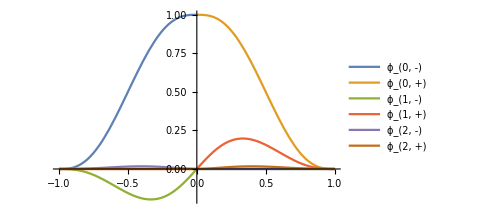

```mathematica
Plot[{ϕ0m[x,0,1]θ[x+1],ϕ0p[x,0,1]θ[x],ϕ1m[x,0,1]θ[x+1],ϕ1p[x,0,1]θ[x],ϕ2m[x,0,1]θ[x+1],ϕ2p[x,0,1]θ[x]},{x,-1,1},PlotRange->Full,ImageSize->Medium,PlotLegends->{"ϕ_(0, -)","ϕ_(0, +)","ϕ_(1, -)","ϕ_(1, +)","ϕ_(2, -)","ϕ_(2, +)"}]
```

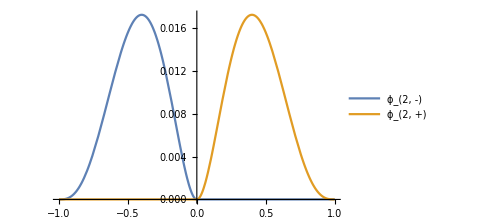

```mathematica
Plot[{ϕ2m[x,0,1]θ[x+1],ϕ2p[x,0,1]θ[x]},{x,-1,1},PlotRange->Full,ImageSize->Medium,PlotLegends->{"ϕ_(2, -)","ϕ_(2, +)"}]
```

```mathematica
FTup[t_]:=Product[Sinc[t 2^-n],{n,1,5}]
up[x_]:=If[Abs[x]≤1,0.5+Sum[FTup[k π]Cos[k π x],{k,1,30}],0]
B3[x_]:=BSplineBasis[3,1/2(x+1)]
```

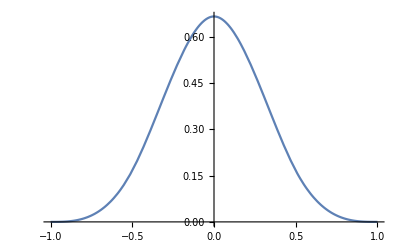

```mathematica
Plot[B3[x],{x,-1,1}]
```

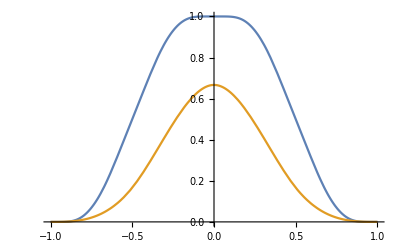

```mathematica
Plot[{up[x],B3[x]},{x,-1,1}]
```

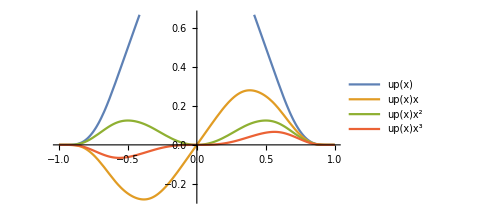

```mathematica
Plot[{up[x],up[x]x,up[x] x^2,up[x] x^3},{x,-1,1},PlotLegends->{"up(x)","up(x)x","up(x)x^2","up(x)x^3"},ImageSize->Medium]
```

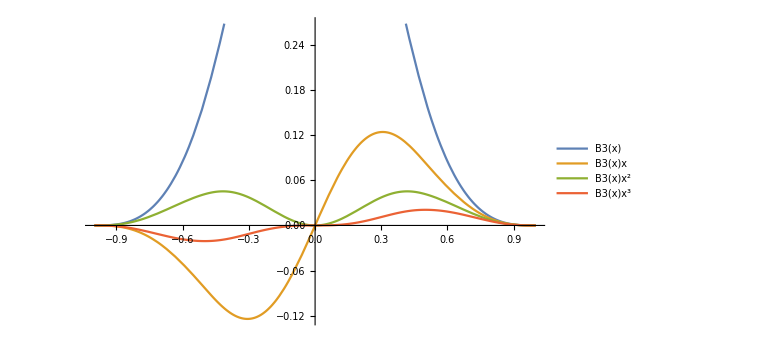

```mathematica
Plot[{B3[x],B3[x]x,B3[x] x^2,B3[x] x^3},{x,-1,1},PlotLegends->{"B3(x)","B3(x)x","B3(x)x^2","B3(x)x^3"},ImageSize->Large]
```

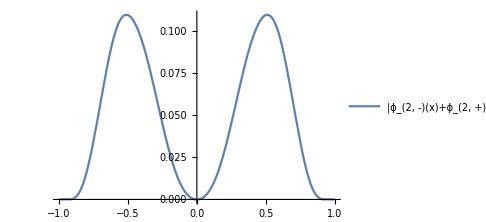

```mathematica
Plot[{Abs[ϕ2m[x,0,1]θ[x+1]+ϕ2p[x,0,1]θ[x]-up[x] x^2]},{x,-1,1},PlotRange->Full,ImageSize->Medium,PlotLegends->{"|ϕ_(2, -)(x)+ϕ_(2, +)(x)-up(x)x^2|"}]
```

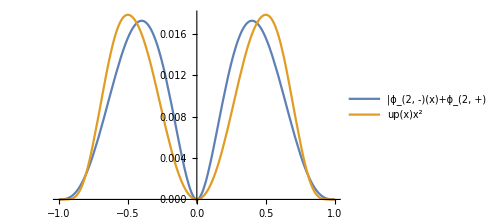

```mathematica
Plot[{ϕ2m[x,0,1]θ[x+1]+ϕ2p[x,0,1]θ[x],1/7 up[x] x^2},{x,-1,1},PlotRange->Full,ImageSize->Medium,PlotLegends->{"|ϕ_(2, -)(x)+ϕ_(2, +)(x)","up(x)x^2"}]
```

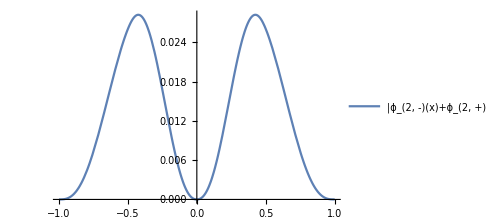

```mathematica
Plot[{Abs[ϕ2m[x,0,1]θ[x+1]+ϕ2p[x,0,1]θ[x]-B3[x] x^2]},{x,-1,1},PlotRange->Full,ImageSize->Medium,PlotLegends->{"|ϕ_(2, -)(x)+ϕ_(2, +)(x)-up(x)x^2|"}]
```

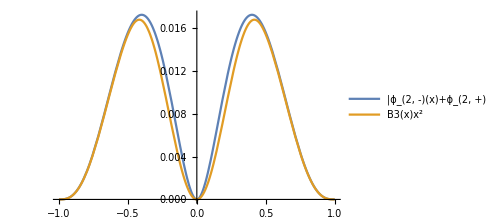

```mathematica
Plot[{ϕ2m[x,0,1]θ[x+1]+ϕ2p[x,0,1]θ[x],1/2.7 B3[x] x^2},{x,-1,1},PlotRange->Full,ImageSize->Medium,PlotLegends->{"|ϕ_(2, -)(x)+ϕ_(2, +)(x)","B3(x)x^2"}]
```

### CIP-BS^0;

```mathematica
ϕ0[x_]:=a+b x
```

#### Constrains;

```mathematica
EqnSys={
ϕ0[-h]==0,
ϕ0[0]==1
};
SolEqnSys=Solve[EqnSys,{a,b}];
ϕ0[x]/.Flatten[SolEqnSys]
EqnSys={
ϕ0[h]==0,
ϕ0[0]==1
};
SolEqnSys=Solve[EqnSys,{a,b}];
ϕ0[x]/.Flatten[SolEqnSys]
```

1+x/h

1-x/h

#### Comparison with cubic B - spline;

```mathematica
ϕ0[x_]:=BSplineBasis[3,1/4(x+2)];
ϕ1[x_]:=1/4 (4 BSplineBasis[2,0,(2+x)/3]-4 BSplineBasis[2,1,(2+x)/3]);
ϕ2[x_]:=1/4 (4/3 (3 BSplineBasis[1,0,(2+x)/2]-3 BSplineBasis[1,1,(2+x)/2])-4/3 (3 BSplineBasis[1,1,(2+x)/2]-3 BSplineBasis[1,2,(2+x)/2]));
{{ϕ0[-1],ϕ0[0],ϕ0[1]},
{ϕ1[-1],ϕ1[0],ϕ1[1]},
{ϕ2[-1],ϕ2[0],ϕ2[1]}}//Grid
```

1/6 | 2/3 | 1/6
1/2 | 0 | -1/2
1 | -2 | 1

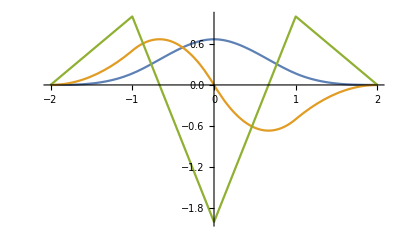

```mathematica
Plot[{ϕ0[x],ϕ1[x],ϕ2[x]},{x,-2,2}]
```